```mathematica
items={"Student ID","I READ the THEORY on the slides", "I WATCHED the VIDEOS","I COMPLETED the SIMULATIONS","I COMPLETED the online QUIZZES","When I did the pre-class assignment, I usually:","When you did the pre-class assignment, what MOTIVATED you to do so?","I found the THEORY on the slides included in the pre-class \n assignments to be HELPFUL for my learning of physics",
"I found the VIDEOS included in the pre-class \n assignments to be HELPFUL for my learning of physics",
"I found the SIMULATIONS included in the pre-class assignments \n to be HELPFUL for my learning of physics",
"OVERALL,I found the pre-class assignments to be HELPFUL \n for my learning of physics",
"How much time did you spend on average completing \n the pre-class assignments and quiz?",
"Did you BUY/RENT A TEXTBOOK for this class?",
"How often did you read the TEXTBOOK to complete \n the PRE-CLASS ASSIGNMENTS?",
"Rate your agreement with the statement: I found \n reading the TEXTBOOK HELPFUL for my learning of physics.",
"Did you use any OTHER RESOURCES to complete \n the PRE-CLASS ASSIGNMENTS?",
"What OTHER RESOURCES did you use to complete the PRE-CLASS ASSIGNMENTS?",
"How often did you use OTHER RESOURCES to complete \n the PRE-CLASS ASSIGNMENTS?",
"Rate your agrement with the statement: I found using \n OTHER RESOURCES HELPFUL for my learning of physics."};
```

```mathematica
frequency={"Rarely","Less than \n half the time","About half \n the time","Most of \n the time","All the \n time"};
agreement={"Strongly \n disagree","Disagree","Neither agree \n nor disagree","Agree","Strongly \n agree"};
time={"0","15 min","30 min","45 min","1 hour","1.5 hours","More than \n 1.5 hours"};
yesno={"yes","no"};
```

```mathematica
options={a,b,c,d,e,f,g};
```

```mathematica
SetDirectory["/Users/christos/Desktop/TEACHING/COURSES/PHYS-175-176/2019-SPRING-PHYS-176/ASSESSMENT/PRECLASS-ASSIGNMENTS/DATA"];
files=FileNames["student-*"];
```

```mathematica
data=Table[{},Length[files]];
For[i=1,i≤Length[files],i++,
data[[i]]=ReadList[files[[i]],Word,WordSeparators->"\n"];
];
data=Sort[data,#1[[1]]<#2[[1]]&];
```

```mathematica
SetDirectory["/Users/christos/Desktop/TEACHING/COURSES/PHYS-175-176/2019-SPRING-PHYS-176/ASSESSMENT/PRECLASS-ASSIGNMENTS"];
```

```mathematica
nitems=14;
item=Table[{},nitems];
For[n=1,n≤nitems-2,n++,
item[[n]]=Table[ToExpression[data[[i,n]]],{i,1,Length[data]}];
];
For[n=nitems-1,n≤nitems,n++,
item[[n]]=Table[data[[i,n]],{i,1,Length[data]}];
];
```

A different way to do the plot without the empty columns

```mathematica
(* n=2;
tallydata=SortBy[Tally[item[[n]]],First];
BarChart[tallydata[[All,2]],ChartLabels->Table[frequency[[i]],{i,Flatten[tallydata[[All,1]]]}],Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}] *)
```

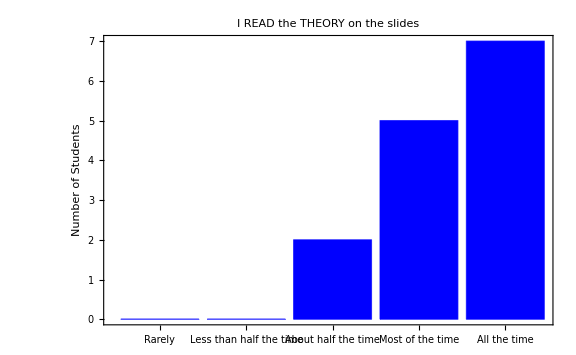

```mathematica
n=2;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->frequency,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["2-theory-frequency.pdf",%];
```

```mathematica
(* n=3;
tallydata=SortBy[Tally[item[[n]]],First];
BarChart[tallydata[[All,2]],ChartLabels->Table[frequency[[i]],{i,Flatten[tallydata[[All,1]]]}],Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}] *)
```

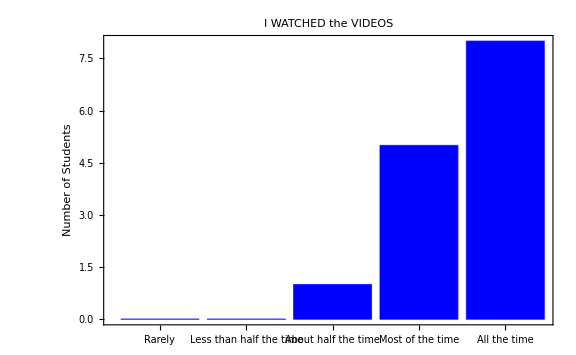

```mathematica
n=3;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->frequency,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["3-videos-frequency.pdf",%];
```

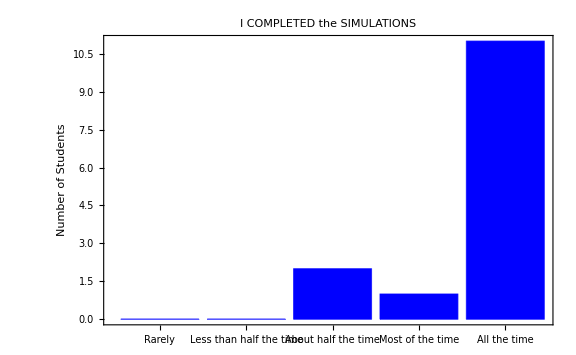

```mathematica
n=4;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->frequency,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["4-simulations-frequency.pdf",%];
```

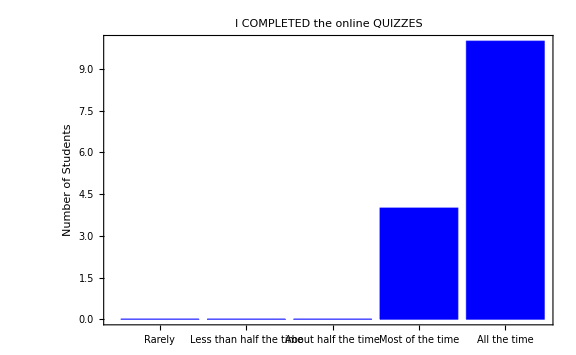

```mathematica
n=5;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->frequency,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["5-quiz-frequency.pdf",%];
```

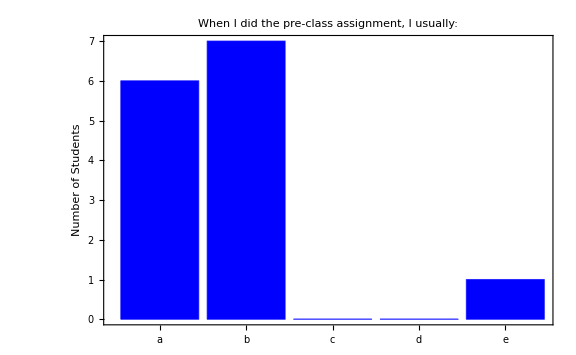

```mathematica
n=6;
dataplot=Table[Count[item[[n]],options[[i]]],{i,1,5}];
BarChart[dataplot,ChartLabels->options,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["6-method.pdf",%];
```

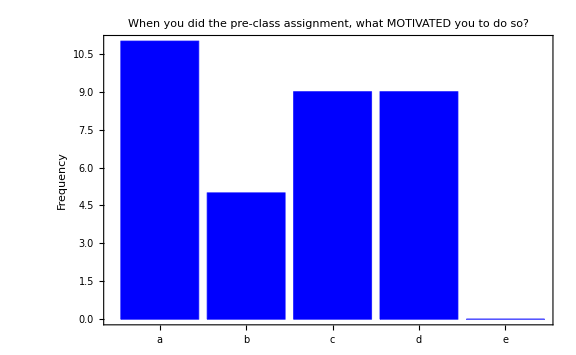

```mathematica
n=7;
dataplot=Table[Count[ToExpression[Flatten[Table[StringSplit[ToString[item[[n,j]]]],{j,1,Length[item[[n]]]}]]],options[[i]]],{i,1,5}];
BarChart[dataplot,ChartLabels->options,Frame->True,FrameLabel->{"","Frequency"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["7-motivation.pdf",%];
```

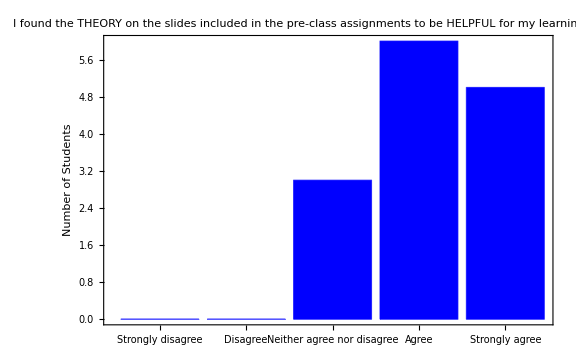

```mathematica
n=8;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->agreement,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["8-theory.pdf",%];
```

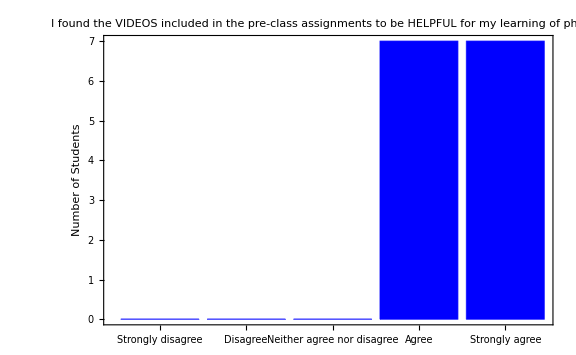

```mathematica
n=9;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->agreement,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["9-videos.pdf",%];
```

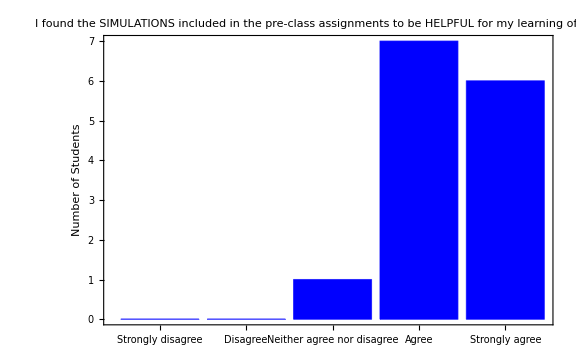

```mathematica
n=10;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->agreement,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",15,GrayLevel[0],Bold}]
```

```mathematica
Export["10-simulations.pdf",%];
```

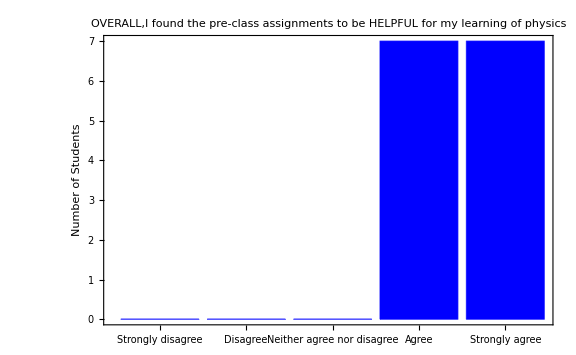

```mathematica
n=11;
dataplot=Table[Count[item[[n]],i],{i,1,5}];
BarChart[dataplot,ChartLabels->agreement,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",15,GrayLevel[0],Bold}]
```

```mathematica
Export["11-overall.pdf",%];
```

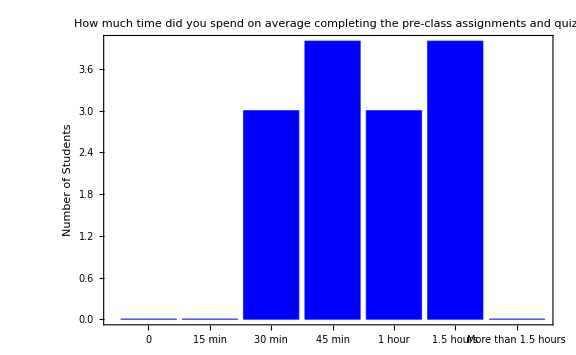

```mathematica
n=12;
dataplot=Table[Count[item[[n]],options[[i]]],{i,1,7}];
BarChart[dataplot,ChartLabels->time,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["12-time.pdf",%];
```

```mathematica
aorb[n_,j_]:=StringTake[item[[n,j]],1]
```

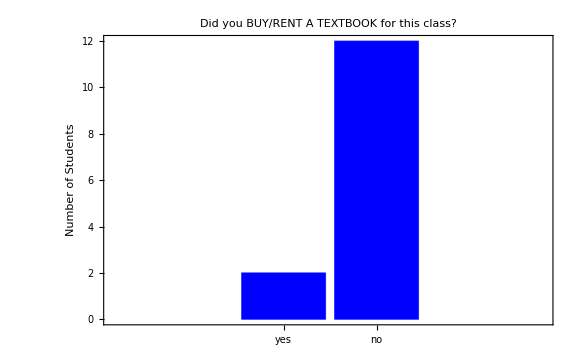

```mathematica
n=13;
dataplot=Table[Count[Table[ToExpression[aorb[n,j]],{j,1,Length[item[[n]]]}],options[[i]]],{i,1,2}];
BarChart[dataplot,ChartLabels->yesno,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["13-textbook.pdf",%];
```

If you want to see the cases

```mathematica
(* StringCases[item[[13]],"a "~~"a"~~" "~~_] *)
```

For counting how many students chose a on the first sub question

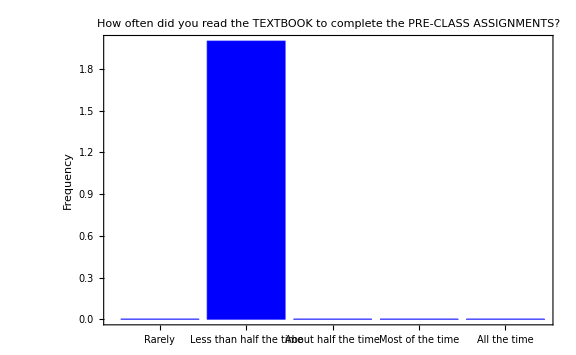

```mathematica
n=14;
dataplot=Table[Count[StringCount[item[[13]],"a "~~ToString[options[[i]]]~~" "~~_],1],{i,1,5}];
BarChart[dataplot,ChartLabels->frequency,Frame->True,FrameLabel->{"","Frequency"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["14-read-textbook.pdf",%];
```

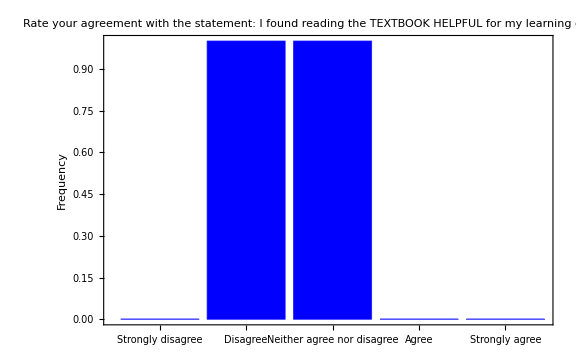

```mathematica
n=15;
dataplot=Table[Count[StringCount[item[[13]],"a "~~_~~" "~~ToString[options[[i]]]],1],{i,1,5}];
BarChart[dataplot,ChartLabels->agreement,Frame->True,FrameLabel->{"","Frequency"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["15-textbook-helpful.pdf",%];
```

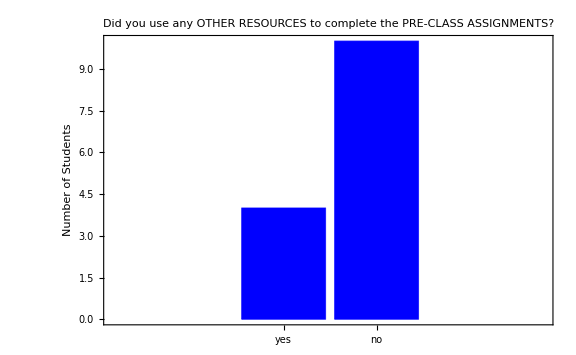

```mathematica
n=14;
dataplot=Table[Count[Table[ToExpression[StringTake[item[[n,j]],1]],{j,1,Length[item[[n]]]}],options[[i]]],{i,1,2}];
BarChart[dataplot,ChartLabels->yesno,Frame->True,FrameLabel->{"","Number of Students"},PlotLabel->items[[n+2]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["16-other-resources.pdf",%];
```

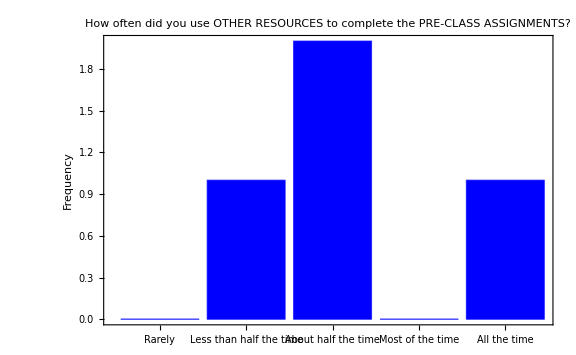

```mathematica
n=18;
dataplot=Table[Count[StringCount[item[[14]],"a "~~ToString[options[[i]]]~~" "~~_],1],{i,1,5}];
BarChart[dataplot,ChartLabels->frequency,Frame->True,FrameLabel->{"","Frequency"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["18-other-resources-frequency.pdf",%];
```

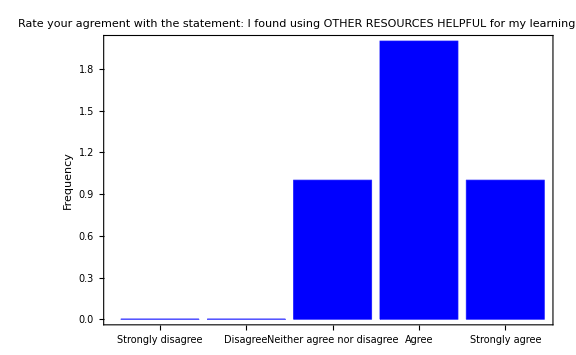

```mathematica
n=19;
dataplot=Table[Count[StringCount[item[[14]],"a "~~_~~" "~~ToString[options[[i]]]],1],{i,1,5}];
BarChart[dataplot,ChartLabels->agreement,Frame->True,FrameLabel->{"","Frequency"},PlotLabel->items[[n]],ChartStyle->Blue,ImageSize->Large,LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold}]
```

```mathematica
Export["19-other-resources-helpful.pdf",%];
```

Save the excel file data I get from Blackboard to a Tab delimited Text file (TXT extension) otherwise Mathematica does not recognize the type of the numbers etc

```mathematica
grades=Import["grades.txt","Table"];
grades=Delete[grades,1];
course=Table[grades[[i,4]],{i,1,Length[grades]}];
preclass=Table[grades[[i,5]],{i,1,Length[grades]}];
homework=Table[grades[[i,6]],{i,1,Length[grades]}];
midterms=Table[grades[[i,7]],{i,1,Length[grades]}];
csem=Table[grades[[i,8]],{i,1,Length[grades]}];
groupwork=Table[grades[[i,9]],{i,1,Length[grades]}];
```

```mathematica
data=Transpose[{homework,preclass,midterms,course,csem,groupwork}];
```

```mathematica
Correlation[data,data]//MatrixForm
```

(1. | 0.60812 | 0.392301 | 0.600941 | -0.173331 | 0.72715
0.60812 | 1. | 0.43344 | 0.649378 | 0.0364656 | 0.63858
0.392301 | 0.43344 | 1. | 0.926379 | 0.45913 | 0.472434
0.600941 | 0.649378 | 0.926379 | 1. | 0.440915 | 0.666078
-0.173331 | 0.0364656 | 0.45913 | 0.440915 | 1. | -0.0069786
0.72715 | 0.63858 | 0.472434 | 0.666078 | -0.0069786 | 1.)

```mathematica
{Correlation[homework,preclass],Correlation[homework,midterms]}
```

{0.60812,0.392301}